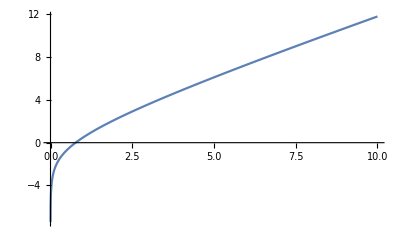

```mathematica
(*Зададим правую часть уравнения и построим ее график*)
f[x_]=x+Log[x]-1/2;
Plot[f[x],{x,0.001,10}]
```

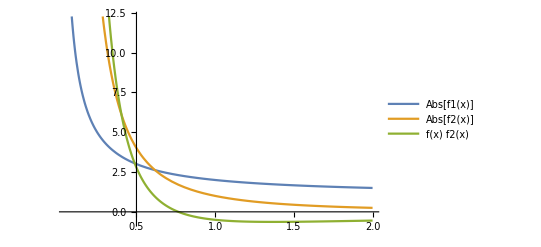

```mathematica
(*Локализуем корень уравнения так, чтобы выполнились все условия теоремы для метода Ньютона*)
a=0.05;
b=2;
(*Найдем производные первого и второго порядка для данной функции*)
f1[x_]=D[f[x],x];
f2[x_]=D[f[x],{x,2}];
Plot[{Abs[f1[x]],Abs[f2[x]],f[x]*f2[x]},{x,a,b},PlotLegends->"Expressions"]
```

```mathematica
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Найдем наибольшее значение модуля производной данной функции на отрезке локализации корня*)
α=MaxValue[{Abs[f1[x]],a≤x≤b},x];
(*Найдем наименьшее значение модуля производной второго порядка данной функции на отрезке локализации корня*)
β=MinValue[{Abs[f2[x]],a≤x≤b},x];
(*Зададим начальное приближение к корню уравнения*)
x0=a;
(*Найдем первую итерацию*)
x1=x0-f[x0]/f1[x0];
(*Зададим переменную для хранения последовательности итерация*)
It={{x0,0},{x1,0}};
(*Зададим переменную для хранения касательных к графику функции*)
Tangent={f[x0]+f1[x0]*(x-x0)};
(*Зададим переменную для подсчёта количества итераций*)
n=1;
(*Реализуем алгоритм метода Ньютона*)
While[α/(2*β)*Abs[x1-x0]^2≥ϵ,
x0=x1;
x1=x0-f[x0]/f1[x0];
It=AppendTo[It,{x1,0}];
Tangent=AppendTo[Tangent,{f[x0]+f1[x0]*(x-x0)}];
n=n+1;
]
Print["Корень уравнения равен: ",N[x1]]
Print["Количество итераций равно: ",n]
```

Корень уравнения равен: 0.766249

Количество итераций равно: 5

```mathematica
(*Выполним анимацию приближений к корню*)
G=Plot[f[x],{x,a,b},PlotStyle->Yellow];
Animate[Show[G,Plot[Tangent[[k]],{x,a,b}],ListPlot[{It[[k]]},PlotStyle->Red],ListPlot[{{It[[k,1]],f[It[[k,1]]]}},Filling->Axis]],{k,1,n,1},AnimationRunning->False]
```